```mathematica
Clear["Global`*"]
```

```mathematica
MatVec[x_]:=Module[{l,M},
l=Length[x];
M={};
For[i=1,i≤l,i++,
M=Join[M,x[[i]]]
];
M
]
```

```mathematica
a=1;b=.8;
xmean=a/(1-b);(*Theoretical mean of the system*)
xvar=1/(1-b^2);(*"Theoretical variance of the system"*)
q=10;(*number of simulated datasets. Should be thought of as number of "tanks"*)
finaltime=300;(*length of each dataset*)
z=100;
comp={};
avg={};

For[o=1,o≤z,o++,

(*"Generate datasets. Stored as simple lists assigned to data[j] where j runs from 1 to q."*)
For[j=1,j≤q,j++,
x0=RandomVariate[NormalDistribution[xmean,Sqrt[xvar]]];(*picks a random starting value from the known distribution*)
data[j]={x0}; (*defines a list with the starting value as its only member. This list will be added to over the rest of the loop*)

(*the following For loop runs the sutoregressive process, generating the data, and stores it in the jth list*)
For[i=1,i≤finaltime,i++,
x0=a+b x0+RandomVariate[NormalDistribution[]];
data[j]=Join[data[j],{x0}]]
];


(*"Estimate parameters a and b from each dataset individually."*)
For[j=1,j≤q,j++,
xmat[j]=Table[{data[j][[i]]},{i,1,finaltime}];(*species vector*)
ymat[j]=Table[{data[j][[i]]},{i,2,finaltime+1}];(*species vector shifted by one time step*)
one=Table[{1},{i,1,finaltime}];(*vector of "ones" needed for the least aquares estimate*)
zmat[j]=Transpose[Join[Transpose[one],Transpose[xmat[j]]]];(*joining the species vector with the "ones" vector*)
dmat[j]=Inverse[Transpose[zmat[j]].zmat[j]].Transpose[zmat[j]].ymat[j](*This is the linear least squares procedure that generates the estimate. The jth estimate is for the jth tank.*)
];

(*Estimate parameters a and b for the composite dataset.*)
onemore={Table[1,{i,1,q*finaltime}]};(*just a longer vector of ones*)
X=MatVec[Table[xmat[j],{j,1,q}]];(*this and the following stack the species vectors on top of each other to make one long vector*)
Y=MatVec[Table[ymat[j],{j,1,q}]];
Z=Transpose[Join[onemore,Transpose[X]]];
DD=Inverse[Transpose[Z].Z].Transpose[Z].Y;(*complete the linear least squares for the composite system*) 


For[j=1,j≤q,j++,
aest[j]=dmat[j][[1,1]];best[j]=dmat[j][[2,1]];(*dmat[j] contains both estimates of "a" and "b" for tank j. This just extracts these estimates and gives them names. These parameters determine totally the estimates stationary distributions.*)
meanest[j]=aest[j]/(1-best[j]);(*mean of the stationary dist. estimated from tank j.*)
varest[j]=1/(1-(best[j])^2);(*variance of stationary dist estimated from tank j*)
];



(*Below we find estimates of paramters "a" and "b" by averging the estimated paramters from each tank*)
aavg=Mean[Table[aest[j],{j,1,q}]];
bavg=Mean[Table[best[j],{j,1,q}]];
meanavg=aavg/(1-bavg);(*the mean of the stationary dist defined by averaged paramteres*)
varavg=1/(1-bavg^2);(*variance of the stationary dist defined by the averaged parameters.*)


acomp=DD[[1,1]];bcomp=DD[[2,1]];
meancomp=acomp/(1-bcomp);
varcomp=1/(1-(bcomp)^2);

comp=Join[comp,{{meancomp,varcomp}}];
avg=Join[avg,{{meanavg,varavg}}];

]
```

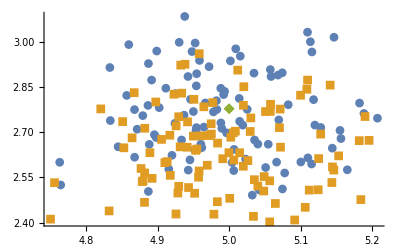

```mathematica
ListPlot[{comp,avg,{{xmean,xvar}}},PlotMarkers->Automatic]
```